```mathematica
coeff=Import["/home/johann/Documents/Projects/hobby/Function_optimization/test.dat","Table",HeaderLines->1];
smallOnes = TakeSmallest[coeff[[All,Length[coeff[[1]]]]],1];
minEps={};
Do[AppendTo[minEps,Position[coeff,smallOnes[[i]]]],{i,Length[smallOnes]}]
```

```mathematica
i=1;
c=coeff[[minEps[[i,1,1]],;;Length[coeff[[1]]]-1]]
coeff[[minEps[[i,1,1]]]]
```

{2.06773,0.597593,-1.28398,0.439254,1.14702}

{2.06773,0.597593,-1.28398,0.439254,1.14702,0.00075006}

```mathematica
besselK1[x_]:=Exp[-x]*(1+1/x)/(c[[2]]*x^(c[[1]]/5)+c[[3]]*x^(c[[1]]/4)+c[[4]]*x^(c[[1]]/3)+c[[5]]*x^(c[[1]]/2)+(2*x/Pi)^c[[1]]+1)^(1/(2*c[[1]]));
b1[x_]:=BesselK[1,x];
```

```mathematica
besselK2[x_]:=Exp[-x]*(1+c[[6]]/x+2/x^2)/(c[[2]]*x^(c[[1]]/5)+c[[3]]*x^(c[[1]]/4)+c[[4]]*x^(c[[1]]/3)+c[[5]]*x^(c[[1]]/2)+(2*x/Pi)^c[[1]]+1)^(1/(2*c[[1]]));
b2[x_]:=BesselK[2,x];
```

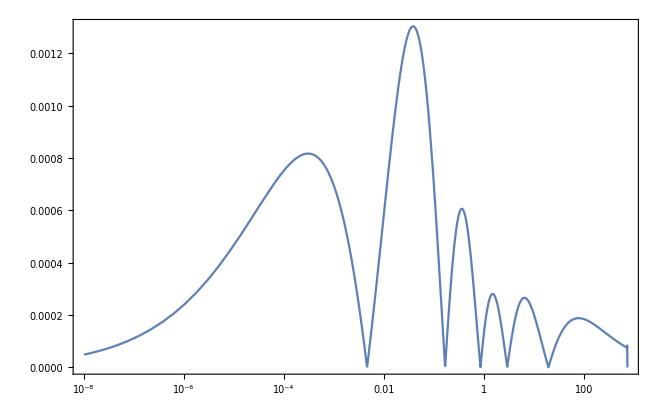

```mathematica
LogLinearPlot[{Abs[besselK1[x]/b1[x]-1]},{x,10^-8,1000},PlotTheme->"FrameGrid",PlotRange->All]
```

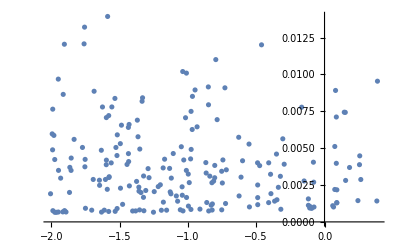

```mathematica
ListPlot[coeff[[All,{3,6}]],PlotRange->All]
```

```mathematica
D[Exp[-x]*(1+c5/x+2/x^2)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c0]//FullSimplify
D[Exp[-x]*(1+c5/x+2/x^2)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c1]
D[Exp[-x]*(1+c5/x+2/x^2)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c2]
D[Exp[-x]*(1+c5/x+2/x^2)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c3]
D[Exp[-x]*(1+c5/x+2/x^2)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c4]
D[Exp[-x]*(1+c5/x+2/x^2)/(c1*x^(c0/5)+c2*x^(c0/4)+c3*x^(c0/3)+c4*x^(c0/2)+(2*x/Pi)^c0+1)^(1/(2*c0)),c5]
```

1/(2 c0^2 x^2)ⅇ^-x (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1/2/c0) (2+x (c5+x)) (-(c0 ((12 c1 x^(c0/5)+15 c2 x^(c0/4)+20 c3 x^(c0/3)+30 c4 x^(c0/2)) Log[x]+15 2^(2+c0) π^-c0 x^c0 Log[(2 x)/π]))/(60 (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0))+Log[1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0])

-(ⅇ^-x (1+2/x^2+c5/x) x^(c0/5) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+2/x^2+c5/x) x^(c0/4) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+2/x^2+c5/x) x^(c0/3) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

-(ⅇ^-x (1+2/x^2+c5/x) x^(c0/2) (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1-1/(2 c0)))/(2 c0)

(ⅇ^-x (1+c1 x^(c0/5)+c2 x^(c0/4)+c3 x^(c0/3)+c4 x^(c0/2)+(2/π)^c0 x^c0)^(-1/2/c0))/x

```mathematica
pos = 10;
```

```mathematica
c[[1]]
```

{1.81698,1.56002,1.18802,1.64199,-1.20877,0.347097}

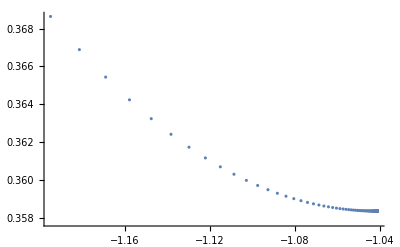

```mathematica
Show[ListPlot[c[[All,{1,2}]],PlotRange->All](*,Plot[c[[pos,3]]*(x-c[[pos,1]])+c[[pos,2]],{x,0,2}]*)]
```

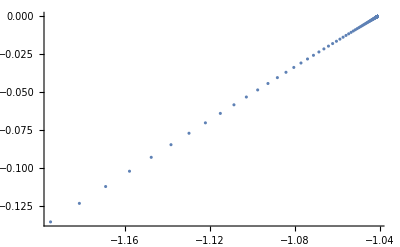

```mathematica
ListPlot[c[[All,{1,3}]],PlotRange->All]
```

```mathematica
c[[1]]
```

{1.81698,1.56002,1.18802,1.64199,-1.20877,0.347097}

```mathematica
c[[Length[c]]]
```

{2.02005,-0.0279336,-0.460926,0.335256,1.04969,0.0109163}